```mathematica
(*Różne zaklęcia w Mathematice.*)
(*Najważniejsza jest funkcja iterate[a , t][{vectors , special}]. Jeżeli t = 1 to działa ona macierzą a na wszystkie wektory w vectors oraz special. Jeżeli t = 0 to nie zmienia wektorów (warto prześledzić jak działa fun).*)
(*Funkcja draw[{vectors , special}] - rysuje wektory na płaszczyźnie. Kropkami rysowane są wektory vectors natomiast strzałeczkami wektory special.*)
```

```mathematica
Options[draw] = {xrange->{-20 , 20} , yrange->{-20 , 20}};
```

```mathematica
fun[a_ , t_][x_]:=t (a.x) +(1 - t)x;
```

```mathematica
iterate[a_ , t_][{vectors:{{_ , _}...},special:{{_ , _}...}}]:={fun[a , t]/@vectors , fun[a , t]/@special};
```

```mathematica
draw[{vectors:{{_ , _}...},special:{{_ , _}...}} , OptionsPattern[]]:= Graphics[{{Black , Point[#]}&/@vectors , {Blue , Arrow[{{0 , 0} , #}]}&/@special} , Axes->True  , PlotRange->{OptionValue[xrange] , OptionValue[yrange]}];
```

```mathematica
(*Koniec zaklęć.*)
```

```mathematica
(*Macierz pojawiająca się w jednym z zadań:*)
```

```mathematica
a = {{4 , -2},{1 , 1}};
```

```mathematica
(*Wartości własne oraz wektory własne a:*)
```

```mathematica
eigen = Eigensystem[a]
```

{{3,2},{{2,1},{1,1}}}

```mathematica
(*Kropkami będą rysowane wektory wskazujące z początku układu współrzędnych do kolejnych punktów na płaszczyźnie:*)
```

```mathematica
vecs = Flatten[Table[{x , y} , {x , -20 , 20 , 1} , {y , -20 , 20 , 1}] , 1];
```

```mathematica
(*Wybrane wektory (wektory własne a) będą rysowane niebieskimi strzałeczkami:*)
```

```mathematica
spec = eigen[[2]];
```

```mathematica
(*Aktualne wartości wektorów:*)
```

```mathematica
current = {vecs , spec};
```

```mathematica
(*Animacja transformacji. t = 0 oznacza działanie macierzy jednostkowej (wektory się nie zmieniają). t = 1 oznacza działanie macierzą a.*)
```

```mathematica
ListAnimate[Table[draw[iterate[a , t]@current] , {t , 0 , 1 , 0.05}] ,AnimationRunning->False]
```

```mathematica
(*Uaktualnienie wektorów:*)
```

```mathematica
current = iterate[a , 1]@current;
```

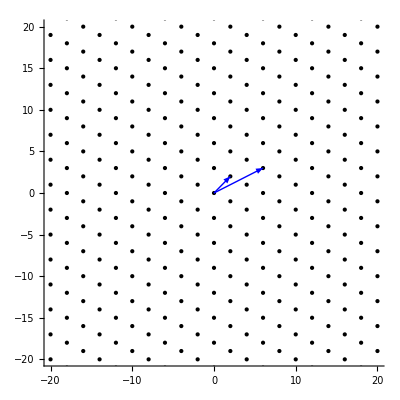

```mathematica
draw[current]
```

```mathematica
(*Kolejna iteracja. Animacja transformacji. t = 0 oznacza działanie macierzy jednostkowej (wektory się nie zmieniają). t = 1 oznacza działanie macierzą a.*)
ListAnimate[Table[draw[iterate[a , t]@current] , {t , 0 , 1 , 0.05}] ,AnimationRunning->False]
```

```mathematica
(*Uaktualnienie wektorów:*)
```

```mathematica
current = iterate[a , 1]@current;
```

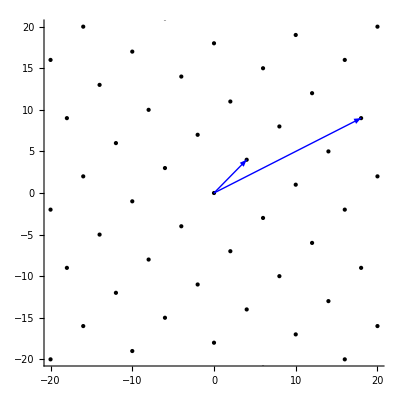

```mathematica
draw[current]
```

```mathematica
s = Transpose[eigen[[2]]];
```

```mathematica
s//MatrixForm
```

(2 | 1
1 | 1)

```mathematica
s.{1 , 0}
```

{2,1}

```mathematica
s.{0 , 1}
```

{1,1}

```mathematica
Inverse[s].a.s//MatrixForm
```

(3 | 0
0 | 2)

```mathematica
(*UWAGA:*)
```

```mathematica
ss = Orthogonalize[eigen[[2]]]
```

{{2/(√5),1/(√5)},{-1/(√5),2/(√5)}}

```mathematica
Inverse[ss].a.ss
```

{{19/5,-3/5},{12/5,6/5}}

```mathematica
ss.a.Inverse[ss]//MatrixForm
```

(3 | -3
0 | 2)